```mathematica
MyList[n_,p_]:=ReadList[StringJoin["d:\\Triangle\\Data\\",ToString[n], "\\",ToString[n],"_",ToString[p],".txt"],Number,2000]
```

```mathematica
MyCoordinateList[n_,p_] := Table[{ MyList[n,p][[i]], p},{i,1,2000}]
```

```mathematica
myGraph[range_, countLines_, maxRoot_] :=
Block[{},
minX =N[ range[[1]][[1]] ];
maxX =N[ range[[1]][[2]] ];
minY= N[ range[[2]][[1]] ];
maxY= N[ range[[2]][[2]] ];
log3 = If[maxRoot==0, IntegerPart[Ceiling[Log[3, maxX]]+1], maxRoot];
Show[
{
Table[
 Plot[{ ((2 x)/(i))^j, ((2x)/(i +1))^j},{x,minX, maxX},
Filling->{1->{2}},
AxesLabel->{"n","p"}, 
PlotRange->range,
GridLines->{Table[k,{k,IntegerPart[Ceiling[minX]], IntegerPart[Floor [maxX]],1}],
Table[k,{k,IntegerPart[Ceiling[minY]], IntegerPart[Floor[maxY]],1}]
},
GridLinesStyle->Blue,
FillingStyle->Directive[Opacity[0.6],ColorData["DarkRainbow"][j]  ]
],
 {i,1,2countLines,2},
  {j,Table[1/l,{l,1,log3   }] }]
}
]]
```

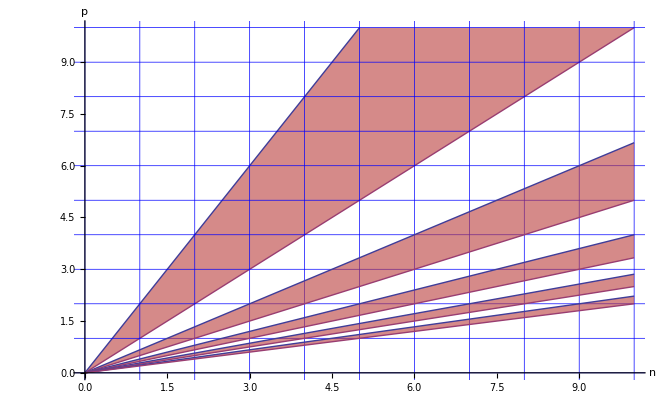

```mathematica
myGraph[{{0,10},{0,10}},5,1]
```